```mathematica
Needs["Notation`"];
Notation[𝓊 ⟺ cu]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,cu,U1,t,t11,t12,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4]}
```

{a^,a[2],a[3],a[4]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†}

```mathematica
vc4 = qszbasisvc[myop]
```

{{{-4,0},{‖▯▯▯▯▯▯▯▯⟩}},{{-3,-1/2},{‖▯▯▯▯▯▯▯▮⟩,‖▯▯▯▯▯▮▯▯⟩,‖▯▯▯▮▯▯▯▯⟩,‖▯▮▯▯▯▯▯▯⟩}},{{-3,1/2},{‖▯▯▯▯▯▯▮▯⟩,‖▯▯▯▯▮▯▯▯⟩,‖▯▯▮▯▯▯▯▯⟩,‖▮▯▯▯▯▯▯▯⟩}},{{-2,-1},{‖▯▯▯▯▯▮▯▮⟩,‖▯▯▯▮▯▯▯▮⟩,‖▯▯▯▮▯▮▯▯⟩,‖▯▮▯▯▯▯▯▮⟩,‖▯▮▯▯▯▮▯▯⟩,‖▯▮▯▮▯▯▯▯⟩}},{{-2,0},{‖▯▯▯▯▯▯▮▮⟩,‖▯▯▯▯▯▮▮▯⟩,‖▯▯▯▯▮▯▯▮⟩,‖▯▯▯▯▮▮▯▯⟩,‖▯▯▯▮▯▯▮▯⟩,‖▯▯▯▮▮▯▯▯⟩,‖▯▯▮▯▯▯▯▮⟩,‖▯▯▮▯▯▮▯▯⟩,‖▯▯▮▮▯▯▯▯⟩,‖▯▮▯▯▯▯▮▯⟩,‖▯▮▯▯▮▯▯▯⟩,‖▯▮▮▯▯▯▯▯⟩,‖▮▯▯▯▯▯▯▮⟩,‖▮▯▯▯▯▮▯▯⟩,‖▮▯▯▮▯▯▯▯⟩,‖▮▮▯▯▯▯▯▯⟩}},{{-2,1},{‖▯▯▯▯▮▯▮▯⟩,‖▯▯▮▯▯▯▮▯⟩,‖▯▯▮▯▮▯▯▯⟩,‖▮▯▯▯▯▯▮▯⟩,‖▮▯▯▯▮▯▯▯⟩,‖▮▯▮▯▯▯▯▯⟩}},{{-1,-3/2},{‖▯▯▯▮▯▮▯▮⟩,‖▯▮▯▯▯▮▯▮⟩,‖▯▮▯▮▯▯▯▮⟩,‖▯▮▯▮▯▮▯▯⟩}},{{-1,-1/2},{‖▯▯▯▯▯▮▮▮⟩,‖▯▯▯▯▮▮▯▮⟩,‖▯▯▯▮▯▯▮▮⟩,‖▯▯▯▮▯▮▮▯⟩,‖▯▯▯▮▮▯▯▮⟩,‖▯▯▯▮▮▮▯▯⟩,‖▯▯▮▯▯▮▯▮⟩,‖▯▯▮▮▯▯▯▮⟩,‖▯▯▮▮▯▮▯▯⟩,‖▯▮▯▯▯▯▮▮⟩,‖▯▮▯▯▯▮▮▯⟩,‖▯▮▯▯▮▯▯▮⟩,‖▯▮▯▯▮▮▯▯⟩,‖▯▮▯▮▯▯▮▯⟩,‖▯▮▯▮▮▯▯▯⟩,‖▯▮▮▯▯▯▯▮⟩,‖▯▮▮▯▯▮▯▯⟩,‖▯▮▮▮▯▯▯▯⟩,‖▮▯▯▯▯▮▯▮⟩,‖▮▯▯▮▯▯▯▮⟩,‖▮▯▯▮▯▮▯▯⟩,‖▮▮▯▯▯▯▯▮⟩,‖▮▮▯▯▯▮▯▯⟩,‖▮▮▯▮▯▯▯▯⟩}},{{-1,1/2},{‖▯▯▯▯▮▯▮▮⟩,‖▯▯▯▯▮▮▮▯⟩,‖▯▯▯▮▮▯▮▯⟩,‖▯▯▮▯▯▯▮▮⟩,‖▯▯▮▯▯▮▮▯⟩,‖▯▯▮▯▮▯▯▮⟩,‖▯▯▮▯▮▮▯▯⟩,‖▯▯▮▮▯▯▮▯⟩,‖▯▯▮▮▮▯▯▯⟩,‖▯▮▯▯▮▯▮▯⟩,‖▯▮▮▯▯▯▮▯⟩,‖▯▮▮▯▮▯▯▯⟩,‖▮▯▯▯▯▯▮▮⟩,‖▮▯▯▯▯▮▮▯⟩,‖▮▯▯▯▮▯▯▮⟩,‖▮▯▯▯▮▮▯▯⟩,‖▮▯▯▮▯▯▮▯⟩,‖▮▯▯▮▮▯▯▯⟩,‖▮▯▮▯▯▯▯▮⟩,‖▮▯▮▯▯▮▯▯⟩,‖▮▯▮▮▯▯▯▯⟩,‖▮▮▯▯▯▯▮▯⟩,‖▮▮▯▯▮▯▯▯⟩,‖▮▮▮▯▯▯▯▯⟩}},{{-1,3/2},{‖▯▯▮▯▮▯▮▯⟩,‖▮▯▯▯▮▯▮▯⟩,‖▮▯▮▯▯▯▮▯⟩,‖▮▯▮▯▮▯▯▯⟩}},{{0,-2},{‖▯▮▯▮▯▮▯▮⟩}},{{0,-1},{‖▯▯▯▮▯▮▮▮⟩,‖▯▯▯▮▮▮▯▮⟩,‖▯▯▮▮▯▮▯▮⟩,‖▯▮▯▯▯▮▮▮⟩,‖▯▮▯▯▮▮▯▮⟩,‖▯▮▯▮▯▯▮▮⟩,‖▯▮▯▮▯▮▮▯⟩,‖▯▮▯▮▮▯▯▮⟩,‖▯▮▯▮▮▮▯▯⟩,‖▯▮▮▯▯▮▯▮⟩,‖▯▮▮▮▯▯▯▮⟩,‖▯▮▮▮▯▮▯▯⟩,‖▮▯▯▮▯▮▯▮⟩,‖▮▮▯▯▯▮▯▮⟩,‖▮▮▯▮▯▯▯▮⟩,‖▮▮▯▮▯▮▯▯⟩}},{{0,0},{‖▯▯▯▯▮▮▮▮⟩,‖▯▯▯▮▮▯▮▮⟩,‖▯▯▯▮▮▮▮▯⟩,‖▯▯▮▯▯▮▮▮⟩,‖▯▯▮▯▮▮▯▮⟩,‖▯▯▮▮▯▯▮▮⟩,‖▯▯▮▮▯▮▮▯⟩,‖▯▯▮▮▮▯▯▮⟩,‖▯▯▮▮▮▮▯▯⟩,‖▯▮▯▯▮▯▮▮⟩,‖▯▮▯▯▮▮▮▯⟩,‖▯▮▯▮▮▯▮▯⟩,‖▯▮▮▯▯▯▮▮⟩,‖▯▮▮▯▯▮▮▯⟩,‖▯▮▮▯▮▯▯▮⟩,‖▯▮▮▯▮▮▯▯⟩,‖▯▮▮▮▯▯▮▯⟩,‖▯▮▮▮▮▯▯▯⟩,‖▮▯▯▯▯▮▮▮⟩,‖▮▯▯▯▮▮▯▮⟩,‖▮▯▯▮▯▯▮▮⟩,‖▮▯▯▮▯▮▮▯⟩,‖▮▯▯▮▮▯▯▮⟩,‖▮▯▯▮▮▮▯▯⟩,‖▮▯▮▯▯▮▯▮⟩,‖▮▯▮▮▯▯▯▮⟩,‖▮▯▮▮▯▮▯▯⟩,‖▮▮▯▯▯▯▮▮⟩,‖▮▮▯▯▯▮▮▯⟩,‖▮▮▯▯▮▯▯▮⟩,‖▮▮▯▯▮▮▯▯⟩,‖▮▮▯▮▯▯▮▯⟩,‖▮▮▯▮▮▯▯▯⟩,‖▮▮▮▯▯▯▯▮⟩,‖▮▮▮▯▯▮▯▯⟩,‖▮▮▮▮▯▯▯▯⟩}},{{0,1},{‖▯▯▮▯▮▯▮▮⟩,‖▯▯▮▯▮▮▮▯⟩,‖▯▯▮▮▮▯▮▯⟩,‖▯▮▮▯▮▯▮▯⟩,‖▮▯▯▯▮▯▮▮⟩,‖▮▯▯▯▮▮▮▯⟩,‖▮▯▯▮▮▯▮▯⟩,‖▮▯▮▯▯▯▮▮⟩,‖▮▯▮▯▯▮▮▯⟩,‖▮▯▮▯▮▯▯▮⟩,‖▮▯▮▯▮▮▯▯⟩,‖▮▯▮▮▯▯▮▯⟩,‖▮▯▮▮▮▯▯▯⟩,‖▮▮▯▯▮▯▮▯⟩,‖▮▮▮▯▯▯▮▯⟩,‖▮▮▮▯▮▯▯▯⟩}},{{0,2},{‖▮▯▮▯▮▯▮▯⟩}},{{1,-3/2},{‖▯▮▯▮▯▮▮▮⟩,‖▯▮▯▮▮▮▯▮⟩,‖▯▮▮▮▯▮▯▮⟩,‖▮▮▯▮▯▮▯▮⟩}},{{1,-1/2},{‖▯▯▯▮▮▮▮▮⟩,‖▯▯▮▮▯▮▮▮⟩,‖▯▯▮▮▮▮▯▮⟩,‖▯▮▯▯▮▮▮▮⟩,‖▯▮▯▮▮▯▮▮⟩,‖▯▮▯▮▮▮▮▯⟩,‖▯▮▮▯▯▮▮▮⟩,‖▯▮▮▯▮▮▯▮⟩,‖▯▮▮▮▯▯▮▮⟩,‖▯▮▮▮▯▮▮▯⟩,‖▯▮▮▮▮▯▯▮⟩,‖▯▮▮▮▮▮▯▯⟩,‖▮▯▯▮▯▮▮▮⟩,‖▮▯▯▮▮▮▯▮⟩,‖▮▯▮▮▯▮▯▮⟩,‖▮▮▯▯▯▮▮▮⟩,‖▮▮▯▯▮▮▯▮⟩,‖▮▮▯▮▯▯▮▮⟩,‖▮▮▯▮▯▮▮▯⟩,‖▮▮▯▮▮▯▯▮⟩,‖▮▮▯▮▮▮▯▯⟩,‖▮▮▮▯▯▮▯▮⟩,‖▮▮▮▮▯▯▯▮⟩,‖▮▮▮▮▯▮▯▯⟩}},{{1,1/2},{‖▯▯▮▯▮▮▮▮⟩,‖▯▯▮▮▮▯▮▮⟩,‖▯▯▮▮▮▮▮▯⟩,‖▯▮▮▯▮▯▮▮⟩,‖▯▮▮▯▮▮▮▯⟩,‖▯▮▮▮▮▯▮▯⟩,‖▮▯▯▯▮▮▮▮⟩,‖▮▯▯▮▮▯▮▮⟩,‖▮▯▯▮▮▮▮▯⟩,‖▮▯▮▯▯▮▮▮⟩,‖▮▯▮▯▮▮▯▮⟩,‖▮▯▮▮▯▯▮▮⟩,‖▮▯▮▮▯▮▮▯⟩,‖▮▯▮▮▮▯▯▮⟩,‖▮▯▮▮▮▮▯▯⟩,‖▮▮▯▯▮▯▮▮⟩,‖▮▮▯▯▮▮▮▯⟩,‖▮▮▯▮▮▯▮▯⟩,‖▮▮▮▯▯▯▮▮⟩,‖▮▮▮▯▯▮▮▯⟩,‖▮▮▮▯▮▯▯▮⟩,‖▮▮▮▯▮▮▯▯⟩,‖▮▮▮▮▯▯▮▯⟩,‖▮▮▮▮▮▯▯▯⟩}},{{1,3/2},{‖▮▯▮▯▮▯▮▮⟩,‖▮▯▮▯▮▮▮▯⟩,‖▮▯▮▮▮▯▮▯⟩,‖▮▮▮▯▮▯▮▯⟩}},{{2,-1},{‖▯▮▯▮▮▮▮▮⟩,‖▯▮▮▮▯▮▮▮⟩,‖▯▮▮▮▮▮▯▮⟩,‖▮▮▯▮▯▮▮▮⟩,‖▮▮▯▮▮▮▯▮⟩,‖▮▮▮▮▯▮▯▮⟩}},{{2,0},{‖▯▯▮▮▮▮▮▮⟩,‖▯▮▮▯▮▮▮▮⟩,‖▯▮▮▮▮▯▮▮⟩,‖▯▮▮▮▮▮▮▯⟩,‖▮▯▯▮▮▮▮▮⟩,‖▮▯▮▮▯▮▮▮⟩,‖▮▯▮▮▮▮▯▮⟩,‖▮▮▯▯▮▮▮▮⟩,‖▮▮▯▮▮▯▮▮⟩,‖▮▮▯▮▮▮▮▯⟩,‖▮▮▮▯▯▮▮▮⟩,‖▮▮▮▯▮▮▯▮⟩,‖▮▮▮▮▯▯▮▮⟩,‖▮▮▮▮▯▮▮▯⟩,‖▮▮▮▮▮▯▯▮⟩,‖▮▮▮▮▮▮▯▯⟩}},{{2,1},{‖▮▯▮▯▮▮▮▮⟩,‖▮▯▮▮▮▯▮▮⟩,‖▮▯▮▮▮▮▮▯⟩,‖▮▮▮▯▮▯▮▮⟩,‖▮▮▮▯▮▮▮▯⟩,‖▮▮▮▮▮▯▮▯⟩}},{{3,-1/2},{‖▯▮▮▮▮▮▮▮⟩,‖▮▮▯▮▮▮▮▮⟩,‖▮▮▮▮▯▮▮▮⟩,‖▮▮▮▮▮▮▯▮⟩}},{{3,1/2},{‖▮▯▮▮▮▮▮▮⟩,‖▮▮▮▯▮▮▮▮⟩,‖▮▮▮▮▮▯▮▮⟩,‖▮▮▮▮▮▮▮▯⟩}},{{4,0},{‖▮▮▮▮▮▮▮▮⟩}}}

```mathematica
basisp2 = Select[vc4,#[[1]]=={0,2}&][[1,2]]
```

{‖▮▯▮▯▮▯▮▯⟩}

```mathematica
basisp1 = Select[vc4,#[[1]]=={0,1}&][[1,2]]
```

{‖▯▯▮▯▮▯▮▮⟩,‖▯▯▮▯▮▮▮▯⟩,‖▯▯▮▮▮▯▮▯⟩,‖▯▮▮▯▮▯▮▯⟩,‖▮▯▯▯▮▯▮▮⟩,‖▮▯▯▯▮▮▮▯⟩,‖▮▯▯▮▮▯▮▯⟩,‖▮▯▮▯▯▯▮▮⟩,‖▮▯▮▯▯▮▮▯⟩,‖▮▯▮▯▮▯▯▮⟩,‖▮▯▮▯▮▮▯▯⟩,‖▮▯▮▮▯▯▮▯⟩,‖▮▯▮▮▮▯▯▯⟩,‖▮▮▯▯▮▯▮▯⟩,‖▮▮▮▯▯▯▮▯⟩,‖▮▮▮▯▮▯▯▯⟩}

```mathematica
basis00 = Select[vc4,#[[1]]=={0,0}&][[1,2]]
```

{‖▯▯▯▯▮▮▮▮⟩,‖▯▯▯▮▮▯▮▮⟩,‖▯▯▯▮▮▮▮▯⟩,‖▯▯▮▯▯▮▮▮⟩,‖▯▯▮▯▮▮▯▮⟩,‖▯▯▮▮▯▯▮▮⟩,‖▯▯▮▮▯▮▮▯⟩,‖▯▯▮▮▮▯▯▮⟩,‖▯▯▮▮▮▮▯▯⟩,‖▯▮▯▯▮▯▮▮⟩,‖▯▮▯▯▮▮▮▯⟩,‖▯▮▯▮▮▯▮▯⟩,‖▯▮▮▯▯▯▮▮⟩,‖▯▮▮▯▯▮▮▯⟩,‖▯▮▮▯▮▯▯▮⟩,‖▯▮▮▯▮▮▯▯⟩,‖▯▮▮▮▯▯▮▯⟩,‖▯▮▮▮▮▯▯▯⟩,‖▮▯▯▯▯▮▮▮⟩,‖▮▯▯▯▮▮▯▮⟩,‖▮▯▯▮▯▯▮▮⟩,‖▮▯▯▮▯▮▮▯⟩,‖▮▯▯▮▮▯▯▮⟩,‖▮▯▯▮▮▮▯▯⟩,‖▮▯▮▯▯▮▯▮⟩,‖▮▯▮▮▯▯▯▮⟩,‖▮▯▮▮▯▮▯▯⟩,‖▮▮▯▯▯▯▮▮⟩,‖▮▮▯▯▯▮▮▯⟩,‖▮▮▯▯▮▯▯▮⟩,‖▮▮▯▯▮▮▯▯⟩,‖▮▮▯▮▯▯▮▯⟩,‖▮▮▯▮▮▯▯▯⟩,‖▮▮▮▯▯▯▯▮⟩,‖▮▮▮▯▯▮▯▯⟩,‖▮▮▮▮▯▯▯▯⟩}

```mathematica
basisn1 = Select[vc4,#[[1]]=={0,-1}&][[1,2]]
```

{‖▯▯▯▮▯▮▮▮⟩,‖▯▯▯▮▮▮▯▮⟩,‖▯▯▮▮▯▮▯▮⟩,‖▯▮▯▯▯▮▮▮⟩,‖▯▮▯▯▮▮▯▮⟩,‖▯▮▯▮▯▯▮▮⟩,‖▯▮▯▮▯▮▮▯⟩,‖▯▮▯▮▮▯▯▮⟩,‖▯▮▯▮▮▮▯▯⟩,‖▯▮▮▯▯▮▯▮⟩,‖▯▮▮▮▯▯▯▮⟩,‖▯▮▮▮▯▮▯▯⟩,‖▮▯▯▮▯▮▯▮⟩,‖▮▮▯▯▯▮▯▮⟩,‖▮▮▯▮▯▯▯▮⟩,‖▮▮▯▮▯▮▯▯⟩}

```mathematica
basisn2 = Select[vc4,#[[1]]=={0,-2}&][[1,2]]
```

{‖▯▮▯▮▯▮▯▮⟩}

```mathematica
basis00//Dimensions
```

{36}

```mathematica
basisp1//Dimensions
```

{16}

```mathematica
1+16+36+1+16
```

70

```mathematica
hhop = -t11(hop[a[1],a[3]]+hop[a[2],a[4]])-t12(hop[a[1],a[4]]+hop[a[2],a[3]])
```

-t12 (a_(1↓)^†·a_(4↓)^+a_(1⇑)^†·a_(4⇑)^+a_(2↓)^†·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^+a_(3↓)^†·a_(2↓)^+a_(3⇑)^†·a_(2⇑)^+a_(4↓)^†·a_(1↓)^+a_(4⇑)^†·a_(1⇑)^)-t11 (a_(1↓)^†·a_(3↓)^+a_(1⇑)^†·a_(3⇑)^+a_(2↓)^†·a_(4↓)^+a_(2⇑)^†·a_(4⇑)^+a_(3↓)^†·a_(1↓)^+a_(3⇑)^†·a_(1⇑)^+a_(4↓)^†·a_(2↓)^+a_(4⇑)^†·a_(2⇑)^)

```mathematica
hhU = cu(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]])
```

𝓊 (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^)

```mathematica
hhu1 = (cu-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[3],UP],number[a[4],DO]]+nc[number[a[3],DO],number[a[4],UP]])//Simplify
```

(2 𝒿-𝓊) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(3↓)^†·a_(4⇑)^†·a_(3↓)^·a_(4⇑)^+a_(3⇑)^†·a_(4↓)^†·a_(3⇑)^·a_(4↓)^)

```mathematica
hhj1 = (cu-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[3],UP],number[a[4],UP]]+nc[number[a[3],DO],number[a[4],DO]])
```

(-3 𝒿+𝓊) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(3↓)^†·a_(4↓)^†·a_(3↓)^·a_(4↓)^-a_(3⇑)^†·a_(4⇑)^†·a_(3⇑)^·a_(4⇑)^)

```mathematica
hhpj1 = nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,3,UP],a[AN,3,DO],a[CR,4,DO],a[AN,4,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(3⇑)^†·a_(4↓)^†·a_(3↓)^·a_(4⇑)^

```mathematica
hhpj = (-cj)(conj[hhpj1]+hhpj1)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(3↓)^†·a_(4⇑)^†·a_(3⇑)^·a_(4↓)^-a_(3⇑)^†·a_(4↓)^†·a_(3↓)^·a_(4⇑)^)

```mathematica
hfj1 = nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,3,UP],a[AN,4,UP],a[CR,3,DO],a[AN,4,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(4↓)^·a_(4⇑)^

```mathematica
hhfj = (-cj)(conj[hfj1]+hfj1)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(4↓)^·a_(4⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(3↓)^·a_(3⇑)^)

```mathematica
ham = hhop+ hhU +hhu1 + hhj1+ hhpj+hhfj//Simplify
```

-t12 (a_(1↓)^†·a_(4↓)^+a_(1⇑)^†·a_(4⇑)^+a_(2↓)^†·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^+a_(3↓)^†·a_(2↓)^+a_(3⇑)^†·a_(2⇑)^+a_(4↓)^†·a_(1↓)^+a_(4⇑)^†·a_(1⇑)^)-t11 (a_(1↓)^†·a_(3↓)^+a_(1⇑)^†·a_(3⇑)^+a_(2↓)^†·a_(4↓)^+a_(2⇑)^†·a_(4⇑)^+a_(3↓)^†·a_(1↓)^+a_(3⇑)^†·a_(1⇑)^+a_(4↓)^†·a_(2↓)^+a_(4⇑)^†·a_(2⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(3↓)^†·a_(4⇑)^†·a_(3⇑)^·a_(4↓)^+a_(3⇑)^†·a_(4↓)^†·a_(3↓)^·a_(4⇑)^)+(2 𝒿-𝓊) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(3↓)^†·a_(4⇑)^†·a_(3↓)^·a_(4⇑)^+a_(3⇑)^†·a_(4↓)^†·a_(3⇑)^·a_(4↓)^)+(3 𝒿-𝓊) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(3↓)^†·a_(4↓)^†·a_(3↓)^·a_(4↓)^+a_(3⇑)^†·a_(4⇑)^†·a_(3⇑)^·a_(4⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(4↓)^·a_(4⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(3↓)^·a_(3⇑)^)-𝓊 (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^)

```mathematica
mybasis = {basisp2,basisp1,basis00,basisn1,basisn2}//Flatten
```

{‖▮▯▮▯▮▯▮▯⟩,‖▯▯▮▯▮▯▮▮⟩,‖▯▯▮▯▮▮▮▯⟩,‖▯▯▮▮▮▯▮▯⟩,‖▯▮▮▯▮▯▮▯⟩,‖▮▯▯▯▮▯▮▮⟩,‖▮▯▯▯▮▮▮▯⟩,‖▮▯▯▮▮▯▮▯⟩,‖▮▯▮▯▯▯▮▮⟩,‖▮▯▮▯▯▮▮▯⟩,‖▮▯▮▯▮▯▯▮⟩,‖▮▯▮▯▮▮▯▯⟩,‖▮▯▮▮▯▯▮▯⟩,‖▮▯▮▮▮▯▯▯⟩,‖▮▮▯▯▮▯▮▯⟩,‖▮▮▮▯▯▯▮▯⟩,‖▮▮▮▯▮▯▯▯⟩,‖▯▯▯▯▮▮▮▮⟩,‖▯▯▯▮▮▯▮▮⟩,‖▯▯▯▮▮▮▮▯⟩,‖▯▯▮▯▯▮▮▮⟩,‖▯▯▮▯▮▮▯▮⟩,‖▯▯▮▮▯▯▮▮⟩,‖▯▯▮▮▯▮▮▯⟩,‖▯▯▮▮▮▯▯▮⟩,‖▯▯▮▮▮▮▯▯⟩,‖▯▮▯▯▮▯▮▮⟩,‖▯▮▯▯▮▮▮▯⟩,‖▯▮▯▮▮▯▮▯⟩,‖▯▮▮▯▯▯▮▮⟩,‖▯▮▮▯▯▮▮▯⟩,‖▯▮▮▯▮▯▯▮⟩,‖▯▮▮▯▮▮▯▯⟩,‖▯▮▮▮▯▯▮▯⟩,‖▯▮▮▮▮▯▯▯⟩,‖▮▯▯▯▯▮▮▮⟩,‖▮▯▯▯▮▮▯▮⟩,‖▮▯▯▮▯▯▮▮⟩,‖▮▯▯▮▯▮▮▯⟩,‖▮▯▯▮▮▯▯▮⟩,‖▮▯▯▮▮▮▯▯⟩,‖▮▯▮▯▯▮▯▮⟩,‖▮▯▮▮▯▯▯▮⟩,‖▮▯▮▮▯▮▯▯⟩,‖▮▮▯▯▯▯▮▮⟩,‖▮▮▯▯▯▮▮▯⟩,‖▮▮▯▯▮▯▯▮⟩,‖▮▮▯▯▮▮▯▯⟩,‖▮▮▯▮▯▯▮▯⟩,‖▮▮▯▮▮▯▯▯⟩,‖▮▮▮▯▯▯▯▮⟩,‖▮▮▮▯▯▮▯▯⟩,‖▮▮▮▮▯▯▯▯⟩,‖▯▯▯▮▯▮▮▮⟩,‖▯▯▯▮▮▮▯▮⟩,‖▯▯▮▮▯▮▯▮⟩,‖▯▮▯▯▯▮▮▮⟩,‖▯▮▯▯▮▮▯▮⟩,‖▯▮▯▮▯▯▮▮⟩,‖▯▮▯▮▯▮▮▯⟩,‖▯▮▯▮▮▯▯▮⟩,‖▯▮▯▮▮▮▯▯⟩,‖▯▮▮▯▯▮▯▮⟩,‖▯▮▮▮▯▯▯▮⟩,‖▯▮▮▮▯▮▯▯⟩,‖▮▯▯▮▯▮▯▮⟩,‖▮▮▯▯▯▮▯▮⟩,‖▮▮▯▮▯▯▯▮⟩,‖▮▮▯▮▯▮▯▯⟩,‖▯▮▯▮▯▮▯▮⟩}

```mathematica
mybasis//Dimensions
```

{70}

```mathematica
basis00//Dimensions
```

{36}

```mathematica
td = {cj->cu/5,cu->6,t12->x t11,t11->0.5}
```

{𝒿→𝓊/5,𝓊→6,t12→t11 x,t11→0.5}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td
```

{{24/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,12,0,-0.5,0.5 x,0,0,0,0.5,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,12,0.5 x,-0.5,0,0,0,0,0.5,0,0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-0.5,0.5 x,42/5,0,0,0,0,0,0,0,0,-0.5,0.5 x,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.5 x,-0.5,0,6,0,0,-6/5,0,0,0,0,0,0,0,-0.5,0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,12,0,-0.5,-0.5 x,0,0.5,0,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,12,0.5 x,0,-0.5 x,0,-0.5,0,0,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-6/5,-0.5,0.5 x,6,0,0,0,0,0.5 x,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.5,0,0,0,-0.5 x,0,0,42/5,0,0,-6/5,0.5,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.5,0,0,0,-0.5 x,0,0,6,-6/5,0,-0.5 x,0,0,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-0.5 x,0,0,0,0.5,0,0,0,-6/5,6,0,0,0.5,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.5 x,0,0,0,-0.5,0,-6/5,0,0,42/5,0,0.5 x,0,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-0.5,0,0,0,0.5 x,0.5,-0.5 x,0,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0.5 x,0,0,0,-0.5,0,0,0.5,0.5 x,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-6/5,0,-0.5 x,0.5,0,0,0,0,0,0,0,42/5,-0.5 x,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-0.5,0,0,0,-0.5 x,0.5,0,0,0,0,-0.5 x,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.5 x,0,0,0,0,0,-0.5 x,-0.5,0,0,0.5,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24,0.5 x,0.5,-0.5 x,-0.5,0,0,0,0,0.5,0.5 x,0,0,0,0,0,0,0,-0.5,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,12,0,0,0,0.5 x,0,-0.5,0,0,0,0.5 x,0,0,0,0,0,0,0,0,0.5,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,12,0,0,0,0.5 x,0,0.5,0,0,-0.5,0,0,0,0,0,0,0,0,0,0.5,0,0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5 x,0,0,12,0,-0.5 x,-0.5,0,0,0,0,0,0.5,0.5 x,0,0,0,0,0,0,0,0,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0,12,0,0,0.5 x,-0.5,0,0,0,0,0,-0.5,0.5 x,0,0,0,0,0,0,0,0,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,-0.5 x,0,12,0,0,-6/5,0,0,0,0,0,0,0,0.5 x,0,0,0,0,0,0,0,0,-0.5 x,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,-0.5,0,0,48/5,-6/5,0,0,0,0,0,0,0,0,-0.5,0,0,0,0,0,0,0,0,0,0.5 x,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0.5 x,0,-6/5,48/5,0,0,0,0,0,0,0,0,0,0.5 x,0,0,0,0,0,0,0,-0.5,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,-0.5,-6/5,0,0,12,0,0,0,0,0,0,0,0,0.5,0,0,0,0,0,0,0,0,-0.5,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,0,0,0,0,0,0,0,12,0,-0.5,-0.5 x,0,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,0,0,0,0,0,0,0,12,0.5 x,0,-0.5 x,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,-0.5,0,0,0,0,0,0,-0.5,0.5 x,24/5,0,0,0,0,0.5 x,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,0,0,0,0,-0.5 x,0,0,48/5,0,0,-6/5,0.5,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,0,0,0,0,-0.5 x,0,0,36/5,-6/5,0,-0.5 x,0,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0,0,0.5,0,0,0,-6/5,36/5,0,0,0.5,0,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,0,0,0,-0.5,0,-6/5,0,0,48/5,0,0.5 x,0,0,0,0,0,-6/5,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,-0.5,0,0,0,0,0.5 x,0.5,-0.5 x,0,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0.5,0,0,-0.5,0,0,0.5,0.5 x,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,-0.5 x,-0.5,0,0,0.5,0,0,-0.5,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0.5 x,-0.5,-0.5 x,0,0,0,0,0.5,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0,0,-0.5 x,0,48/5,0,0,-6/5,0,0.5,0,0,0,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0,-0.5,0,0,36/5,-6/5,0,0,0,-0.5,0,0,0,0,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0,0.5 x,0,-6/5,36/5,0,0,0.5 x,0,0,0,0,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,-0.5,-6/5,0,0,48/5,0,0,0.5 x,0,0,0,0,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5 x,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,-0.5 x,0,0,0,0,24/5,-0.5 x,0.5,0,0,0,0,0,0,0.5,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5 x,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,0.5 x,0,-0.5 x,12,0,0,0,0,0,0,0,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,0.5 x,0.5,0,12,0,0,0,0,0,0,0,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0.5,0,0,0,0,0,0,0,0,-0.5,0,0,0,0,0,0,0,0,12,0,0,-6/5,0.5,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0,0,0.5,0,0,0,0,0,0,0,-0.5 x,0,0,0,0,0,0,0,0,0,48/5,-6/5,0,-0.5 x,0,0,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,-0.5 x,0,0,0,0,0,0,0,0,0,0.5,0,0,0,0,0,0,0,0,-6/5,48/5,0,0,0.5,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,0,0.5 x,0,0,0,0,0,0,0,0,-0.5 x,0,0,0,0,0,0,0,-6/5,0,0,12,0,0.5 x,0,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0,0,0,0,0,0,-0.5 x,0.5,0,0,0,0,0,0.5,-0.5 x,0,0,12,0,0,0,0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,0,0,0,0,0,0,0,0,-0.5 x,-0.5,0,0,0,0,0,0.5,0.5 x,0,12,0,0,0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5 x,0,-0.5,0,0,0,0,0,0,0,0,0,0.5,0,0,-0.5,0,-0.5 x,0,0,0,12,0,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,-0.5,0,0,0,0,0,0,0,0,-0.5 x,0,0,0,0.5,0,-0.5 x,0,0,0,12,-0.5 x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0.5,0,0,0,0,0,0,0,-0.5 x,-0.5,0,0,0,0,0.5,0.5 x,-0.5,-0.5 x,24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,-0.5,0,0,0.5,0.5 x,0,0,0,0,0,-0.5 x,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0.5 x,0,0,0,0,-0.5,0.5 x,0,0,0,0.5,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0.5 x,42/5,0,0,0,0,0,0,0,-0.5,0.5 x,0,-6/5,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,-0.5 x,-0.5,0,0,0.5,0,0,0,-0.5 x,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0.5 x,-0.5,-0.5 x,0,0,0,0.5,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0,0,-0.5 x,0,42/5,0,0,-6/5,0,0.5,0,0,0,-0.5 x,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,-0.5,0,0,6,-6/5,0,0,0,-0.5,0,0,0,0.5 x,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0.5 x,0,-6/5,6,0,0,0.5 x,0,0,0,-0.5,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,-0.5,-6/5,0,0,42/5,0,0,0.5 x,0,0,0,-0.5,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,-0.5 x,0,0,0,0,6,-0.5 x,0.5,-6/5,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0.5,0,0.5 x,0,-0.5 x,12,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,0,0,-0.5,0,0.5 x,0.5,0,12,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5 x,0.5,0,0,0,0,0,0,0,-6/5,0,0,6,0,0.5,-0.5 x,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/5,-0.5 x,0.5,0,0,0,0,0,0,0,0,42/5,-0.5 x,0.5,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5 x,0,-0.5,0,0,0,0,0.5,-0.5 x,12,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5 x,0,-0.5,0,0,0,-0.5 x,0.5,0,12,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24/5}}

```mathematica
mymat//Dimensions
```

{70,70}

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,3,0.1}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,3,0.1}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,3,0.1}];
```

```mathematica
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,3,0.1}];
```

```mathematica
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,3,0.1}];
```

```mathematica
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,3,0.1}];
```

```mathematica
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,3,0.1}];
```

```mathematica
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,3,0.1}];
```

```mathematica
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,3,0.1}];
```

```mathematica
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.1}];
```

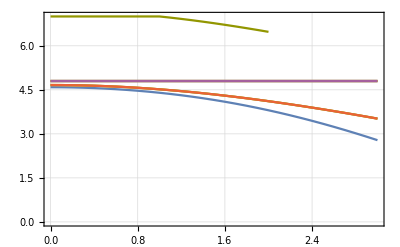

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic,PlotRange->All]
```

```mathematica
Expand[(a1+a2+a3+a4)(a1+a2+a3+a4)]
```

a1^2+2 a1 a2+a2^2+2 a1 a3+2 a2 a3+a3^2+2 a1 a4+2 a2 a4+2 a3 a4+a4^2

```mathematica
S2 = spinspin[a[1],a[1]]+2spinspin[a[1],a[2]]+spinspin[a[2],a[2]]+2spinspin[a[1],a[3]]+2spinspin[a[2],a[3]]+spinspin[a[3],a[3]]+2spinspin[a[1],a[4]]+2spinspin[a[2],a[4]]+2spinspin[a[3],a[4]]+spinspin[a[4],a[4]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(3↓)^†·a_(3↓)^+3 a_(3⇑)^†·a_(3⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+2 a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^-4 a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+2 a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^-2 a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+2 a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^-4 a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-4 a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+2 a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^-2 a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^+6 a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-2 a_(3↓)^†·a_(4↓)^†·a_(3↓)^·a_(4↓)^+2 a_(3↓)^†·a_(4⇑)^†·a_(3↓)^·a_(4⇑)^-4 a_(3↓)^†·a_(4⇑)^†·a_(3⇑)^·a_(4↓)^-4 a_(3⇑)^†·a_(4↓)^†·a_(3↓)^·a_(4⇑)^+2 a_(3⇑)^†·a_(4↓)^†·a_(3⇑)^·a_(4↓)^-2 a_(3⇑)^†·a_(4⇑)^†·a_(3⇑)^·a_(4⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[S2,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,3,0.1}],{j,1,10}]
```

1

-4.93846×10^-17

1

-4.69454×10^-17

1

-9.06624×10^-17

1

-2.05106×10^-16

1

-2.1728×10^-16

1

3.27083×10^-16

1

2.80231×10^-16

1

-2.9521×10^-17

1

-7.51409×10^-17

1

-3.23382×10^-17

1

2.83747×10^-16

1

1.54409×10^-16

1

1.53704×10^-16

1

-4.05606×10^-18

1

-1.4293×10^-16

1

-5.89552×10^-19

1

-4.27324×10^-17

1

5.21431×10^-17

1

5.93597×10^-17

1

-1.53035×10^-16

1

7.82199×10^-17

1

-6.56118×10^-17

1

-1.28867×10^-16

1

-5.40509×10^-17

1

-2.21259×10^-16

1

-1.76536×10^-16

1

-1.21155×10^-16

1

2.93435×10^-16

1

1.16722×10^-16

1

2.12498×10^-16

1

-3.8431×10^-17

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

3

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

4

2.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

5

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

6

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

7

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

8

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

9

6.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

10

2.

```mathematica
data1 //MatrixForm
```

(1 | 0. | -4.93846×10^-17 | 4.589
1 | 0.1 | -4.69454×10^-17 | 4.58714
1 | 0.2 | -9.06624×10^-17 | 4.58158
1 | 0.3 | -2.05106×10^-16 | 4.57228
1 | 0.4 | -2.1728×10^-16 | 4.55924
1 | 0.5 | 3.27083×10^-16 | 4.54241
1 | 0.6 | 2.80231×10^-16 | 4.52176
1 | 0.7 | -2.9521×10^-17 | 4.49725
1 | 0.8 | -7.51409×10^-17 | 4.46883
1 | 0.9 | -3.23382×10^-17 | 4.43643
1 | 1. | 2.83747×10^-16 | 4.4
1 | 1.1 | 1.54409×10^-16 | 4.35948
1 | 1.2 | 1.53704×10^-16 | 4.31482
1 | 1.3 | -4.05606×10^-18 | 4.26596
1 | 1.4 | -1.4293×10^-16 | 4.21285
1 | 1.5 | -5.89552×10^-19 | 4.15544
1 | 1.6 | -4.27324×10^-17 | 4.0937
1 | 1.7 | 5.21431×10^-17 | 4.0276
1 | 1.8 | 5.93597×10^-17 | 3.95714
1 | 1.9 | -1.53035×10^-16 | 3.8823
1 | 2. | 7.82199×10^-17 | 3.80311
1 | 2.1 | -6.56118×10^-17 | 3.71959
1 | 2.2 | -1.28867×10^-16 | 3.63179
1 | 2.3 | -5.40509×10^-17 | 3.53976
1 | 2.4 | -2.21259×10^-16 | 3.44357
1 | 2.5 | -1.76536×10^-16 | 3.34331
1 | 2.6 | -1.21155×10^-16 | 3.23907
1 | 2.7 | 2.93435×10^-16 | 3.13096
1 | 2.8 | 1.16722×10^-16 | 3.01909
1 | 2.9 | 2.12498×10^-16 | 2.90359
1 | 3. | -3.8431×10^-17 | 2.78457
2 | 0. | 2. | 4.66369
2 | 0.1 | 2. | 4.6622
2 | 0.2 | 2. | 4.65774
2 | 0.3 | 2. | 4.65031
2 | 0.4 | 2. | 4.63993
2 | 0.5 | 2. | 4.62664
2 | 0.6 | 2. | 4.61047
2 | 0.7 | 2. | 4.59145
2 | 0.8 | 2. | 4.56964
2 | 0.9 | 2. | 4.54509
2 | 1. | 2. | 4.51786
2 | 1.1 | 2. | 4.488
2 | 1.2 | 2. | 4.45559
2 | 1.3 | 2. | 4.42069
2 | 1.4 | 2. | 4.38338
2 | 1.5 | 2. | 4.34373
2 | 1.6 | 2. | 4.30182
2 | 1.7 | 2. | 4.25772
2 | 1.8 | 2. | 4.2115
2 | 1.9 | 2. | 4.16325
2 | 2. | 2. | 4.11304
2 | 2.1 | 2. | 4.06094
2 | 2.2 | 2. | 4.00703
2 | 2.3 | 2. | 3.95139
2 | 2.4 | 2. | 3.89407
2 | 2.5 | 2. | 3.83515
2 | 2.6 | 2. | 3.7747
2 | 2.7 | 2. | 3.71278
2 | 2.8 | 2. | 3.64945
2 | 2.9 | 2. | 3.58478
2 | 3. | 2. | 3.51882
3 | 0. | 2. | 4.66369
3 | 0.1 | 2. | 4.6622
3 | 0.2 | 2. | 4.65774
3 | 0.3 | 2. | 4.65031
3 | 0.4 | 2. | 4.63993
3 | 0.5 | 2. | 4.62664
3 | 0.6 | 2. | 4.61047
3 | 0.7 | 2. | 4.59145
3 | 0.8 | 2. | 4.56964
3 | 0.9 | 2. | 4.54509
3 | 1. | 2. | 4.51786
3 | 1.1 | 2. | 4.488
3 | 1.2 | 2. | 4.45559
3 | 1.3 | 2. | 4.42069
3 | 1.4 | 2. | 4.38338
3 | 1.5 | 2. | 4.34373
3 | 1.6 | 2. | 4.30182
3 | 1.7 | 2. | 4.25772
3 | 1.8 | 2. | 4.2115
3 | 1.9 | 2. | 4.16325
3 | 2. | 2. | 4.11304
3 | 2.1 | 2. | 4.06094
3 | 2.2 | 2. | 4.00703
3 | 2.3 | 2. | 3.95139
3 | 2.4 | 2. | 3.89407
3 | 2.5 | 2. | 3.83515
3 | 2.6 | 2. | 3.7747
3 | 2.7 | 2. | 3.71278
3 | 2.8 | 2. | 3.64945
3 | 2.9 | 2. | 3.58478
3 | 3. | 2. | 3.51882
4 | 0. | 2. | 4.66369
4 | 0.1 | 2. | 4.6622
4 | 0.2 | 2. | 4.65774
4 | 0.3 | 2. | 4.65031
4 | 0.4 | 2. | 4.63993
4 | 0.5 | 2. | 4.62664
4 | 0.6 | 2. | 4.61047
4 | 0.7 | 2. | 4.59145
4 | 0.8 | 2. | 4.56964
4 | 0.9 | 2. | 4.54509
4 | 1. | 2. | 4.51786
4 | 1.1 | 2. | 4.488
4 | 1.2 | 2. | 4.45559
4 | 1.3 | 2. | 4.42069
4 | 1.4 | 2. | 4.38338
4 | 1.5 | 2. | 4.34373
4 | 1.6 | 2. | 4.30182
4 | 1.7 | 2. | 4.25772
4 | 1.8 | 2. | 4.2115
4 | 1.9 | 2. | 4.16325
4 | 2. | 2. | 4.11304
4 | 2.1 | 2. | 4.06094
4 | 2.2 | 2. | 4.00703
4 | 2.3 | 2. | 3.95139
4 | 2.4 | 2. | 3.89407
4 | 2.5 | 2. | 3.83515
4 | 2.6 | 2. | 3.7747
4 | 2.7 | 2. | 3.71278
4 | 2.8 | 2. | 3.64945
4 | 2.9 | 2. | 3.58478
4 | 3. | 2. | 3.51882
5 | 0. | 6. | 4.8
5 | 0.1 | 6. | 4.8
5 | 0.2 | 6. | 4.8
5 | 0.3 | 6. | 4.8
5 | 0.4 | 6. | 4.8
5 | 0.5 | 6. | 4.8
5 | 0.6 | 6. | 4.8
5 | 0.7 | 6. | 4.8
5 | 0.8 | 6. | 4.8
5 | 0.9 | 6. | 4.8
5 | 1. | 6. | 4.8
5 | 1.1 | 6. | 4.8
5 | 1.2 | 6. | 4.8
5 | 1.3 | 6. | 4.8
5 | 1.4 | 6. | 4.8
5 | 1.5 | 6. | 4.8
5 | 1.6 | 6. | 4.8
5 | 1.7 | 6. | 4.8
5 | 1.8 | 6. | 4.8
5 | 1.9 | 6. | 4.8
5 | 2. | 6. | 4.8
5 | 2.1 | 6. | 4.8
5 | 2.2 | 6. | 4.8
5 | 2.3 | 6. | 4.8
5 | 2.4 | 6. | 4.8
5 | 2.5 | 6. | 4.8
5 | 2.6 | 6. | 4.8
5 | 2.7 | 6. | 4.8
5 | 2.8 | 6. | 4.8
5 | 2.9 | 6. | 4.8
5 | 3. | 6. | 4.8
6 | 0. | 6. | 4.8
6 | 0.1 | 6. | 4.8
6 | 0.2 | 6. | 4.8
6 | 0.3 | 6. | 4.8
6 | 0.4 | 6. | 4.8
6 | 0.5 | 6. | 4.8
6 | 0.6 | 6. | 4.8
6 | 0.7 | 6. | 4.8
6 | 0.8 | 6. | 4.8
6 | 0.9 | 6. | 4.8
6 | 1. | 6. | 4.8
6 | 1.1 | 6. | 4.8
6 | 1.2 | 6. | 4.8
6 | 1.3 | 6. | 4.8
6 | 1.4 | 6. | 4.8
6 | 1.5 | 6. | 4.8
6 | 1.6 | 6. | 4.8
6 | 1.7 | 6. | 4.8
6 | 1.8 | 6. | 4.8
6 | 1.9 | 6. | 4.8
6 | 2. | 6. | 4.8
6 | 2.1 | 6. | 4.8
6 | 2.2 | 6. | 4.8
6 | 2.3 | 6. | 4.8
6 | 2.4 | 6. | 4.8
6 | 2.5 | 6. | 4.8
6 | 2.6 | 6. | 4.8
6 | 2.7 | 6. | 4.8
6 | 2.8 | 6. | 4.8
6 | 2.9 | 6. | 4.8
6 | 3. | 6. | 4.8
7 | 0. | 6. | 4.8
7 | 0.1 | 6. | 4.8
7 | 0.2 | 6. | 4.8
7 | 0.3 | 6. | 4.8
7 | 0.4 | 6. | 4.8
7 | 0.5 | 6. | 4.8
7 | 0.6 | 6. | 4.8
7 | 0.7 | 6. | 4.8
7 | 0.8 | 6. | 4.8
7 | 0.9 | 6. | 4.8
7 | 1. | 6. | 4.8
7 | 1.1 | 6. | 4.8
7 | 1.2 | 6. | 4.8
7 | 1.3 | 6. | 4.8
7 | 1.4 | 6. | 4.8
7 | 1.5 | 6. | 4.8
7 | 1.6 | 6. | 4.8
7 | 1.7 | 6. | 4.8
7 | 1.8 | 6. | 4.8
7 | 1.9 | 6. | 4.8
7 | 2. | 6. | 4.8
7 | 2.1 | 6. | 4.8
7 | 2.2 | 6. | 4.8
7 | 2.3 | 6. | 4.8
7 | 2.4 | 6. | 4.8
7 | 2.5 | 6. | 4.8
7 | 2.6 | 6. | 4.8
7 | 2.7 | 6. | 4.8
7 | 2.8 | 6. | 4.8
7 | 2.9 | 6. | 4.8
7 | 3. | 6. | 4.8
8 | 0. | 6. | 4.8
8 | 0.1 | 6. | 4.8
8 | 0.2 | 6. | 4.8
8 | 0.3 | 6. | 4.8
8 | 0.4 | 6. | 4.8
8 | 0.5 | 6. | 4.8
8 | 0.6 | 6. | 4.8
8 | 0.7 | 6. | 4.8
8 | 0.8 | 6. | 4.8
8 | 0.9 | 6. | 4.8
8 | 1. | 6. | 4.8
8 | 1.1 | 6. | 4.8
8 | 1.2 | 6. | 4.8
8 | 1.3 | 6. | 4.8
8 | 1.4 | 6. | 4.8
8 | 1.5 | 6. | 4.8
8 | 1.6 | 6. | 4.8
8 | 1.7 | 6. | 4.8
8 | 1.8 | 6. | 4.8
8 | 1.9 | 6. | 4.8
8 | 2. | 6. | 4.8
8 | 2.1 | 6. | 4.8
8 | 2.2 | 6. | 4.8
8 | 2.3 | 6. | 4.8
8 | 2.4 | 6. | 4.8
8 | 2.5 | 6. | 4.8
8 | 2.6 | 6. | 4.8
8 | 2.7 | 6. | 4.8
8 | 2.8 | 6. | 4.8
8 | 2.9 | 6. | 4.8
8 | 3. | 6. | 4.8
9 | 0. | 6. | 4.8
9 | 0.1 | 6. | 4.8
9 | 0.2 | 6. | 4.8
9 | 0.3 | 6. | 4.8
9 | 0.4 | 6. | 4.8
9 | 0.5 | 6. | 4.8
9 | 0.6 | 6. | 4.8
9 | 0.7 | 6. | 4.8
9 | 0.8 | 6. | 4.8
9 | 0.9 | 6. | 4.8
9 | 1. | 6. | 4.8
9 | 1.1 | 6. | 4.8
9 | 1.2 | 6. | 4.8
9 | 1.3 | 6. | 4.8
9 | 1.4 | 6. | 4.8
9 | 1.5 | 6. | 4.8
9 | 1.6 | 6. | 4.8
9 | 1.7 | 6. | 4.8
9 | 1.8 | 6. | 4.8
9 | 1.9 | 6. | 4.8
9 | 2. | 6. | 4.8
9 | 2.1 | 6. | 4.8
9 | 2.2 | 6. | 4.8
9 | 2.3 | 6. | 4.8
9 | 2.4 | 6. | 4.8
9 | 2.5 | 6. | 4.8
9 | 2.6 | 6. | 4.8
9 | 2.7 | 6. | 4.8
9 | 2.8 | 6. | 4.8
9 | 2.9 | 6. | 4.8
9 | 3. | 6. | 4.8
10 | 0. | 2. | 7.
10 | 0.1 | 2. | 7.
10 | 0.2 | 2. | 7.
10 | 0.3 | 2. | 7.
10 | 0.4 | 2. | 7.
10 | 0.5 | 2. | 7.
10 | 0.6 | 2. | 7.
10 | 0.7 | 2. | 7.
10 | 0.8 | 2. | 7.
10 | 0.9 | 2. | 7.
10 | 1. | 2. | 7.
10 | 1.1 | 2. | 6.95992
10 | 1.2 | 2. | 6.91672
10 | 1.3 | 2. | 6.87053
10 | 1.4 | 2. | 6.82151
10 | 1.5 | 2. | 6.76981
10 | 1.6 | 2. | 6.71556
10 | 1.7 | 2. | 6.65891
10 | 1.8 | 2. | 6.6
10 | 1.9 | 2. | 6.53895
10 | 2. | 2. | 6.4759
10 | 2.1 | 2. | 6.41096
10 | 2.2 | 2. | 6.34424
10 | 2.3 | 2. | 6.27585
10 | 2.4 | 2. | 6.20589
10 | 2.5 | 2. | 6.13446
10 | 2.6 | 2. | 6.06164
10 | 2.7 | 2. | 5.98752
10 | 2.8 | 2. | 5.91218
10 | 2.9 | 2. | 5.83569
10 | 3. | 2. | 5.75813)

```mathematica
data1//Dimensions
```

{310,4}

```mathematica
tm00 = Flatten[{data1[[1;;31,1;;4]]},1]
```

{{1,0.,-4.93846×10^-17,4.589},{1,0.1,-4.69454×10^-17,4.58714},{1,0.2,-9.06624×10^-17,4.58158},{1,0.3,-2.05106×10^-16,4.57228},{1,0.4,-2.1728×10^-16,4.55924},{1,0.5,3.27083×10^-16,4.54241},{1,0.6,2.80231×10^-16,4.52176},{1,0.7,-2.9521×10^-17,4.49725},{1,0.8,-7.51409×10^-17,4.46883},{1,0.9,-3.23382×10^-17,4.43643},{1,1.,2.83747×10^-16,4.4},{1,1.1,1.54409×10^-16,4.35948},{1,1.2,1.53704×10^-16,4.31482},{1,1.3,-4.05606×10^-18,4.26596},{1,1.4,-1.4293×10^-16,4.21285},{1,1.5,-5.89552×10^-19,4.15544},{1,1.6,-4.27324×10^-17,4.0937},{1,1.7,5.21431×10^-17,4.0276},{1,1.8,5.93597×10^-17,3.95714},{1,1.9,-1.53035×10^-16,3.8823},{1,2.,7.82199×10^-17,3.80311},{1,2.1,-6.56118×10^-17,3.71959},{1,2.2,-1.28867×10^-16,3.63179},{1,2.3,-5.40509×10^-17,3.53976},{1,2.4,-2.21259×10^-16,3.44357},{1,2.5,-1.76536×10^-16,3.34331},{1,2.6,-1.21155×10^-16,3.23907},{1,2.7,2.93435×10^-16,3.13096},{1,2.8,1.16722×10^-16,3.01909},{1,2.9,2.12498×10^-16,2.90359},{1,3.,-3.8431×10^-17,2.78457}}

```mathematica
e0data = Table[{tm00[[i,2]],tm00[[i,4]],tm00[[i,3]]},{i,1,31}]
```

{{0.,4.589,-4.93846×10^-17},{0.1,4.58714,-4.69454×10^-17},{0.2,4.58158,-9.06624×10^-17},{0.3,4.57228,-2.05106×10^-16},{0.4,4.55924,-2.1728×10^-16},{0.5,4.54241,3.27083×10^-16},{0.6,4.52176,2.80231×10^-16},{0.7,4.49725,-2.9521×10^-17},{0.8,4.46883,-7.51409×10^-17},{0.9,4.43643,-3.23382×10^-17},{1.,4.4,2.83747×10^-16},{1.1,4.35948,1.54409×10^-16},{1.2,4.31482,1.53704×10^-16},{1.3,4.26596,-4.05606×10^-18},{1.4,4.21285,-1.4293×10^-16},{1.5,4.15544,-5.89552×10^-19},{1.6,4.0937,-4.27324×10^-17},{1.7,4.0276,5.21431×10^-17},{1.8,3.95714,5.93597×10^-17},{1.9,3.8823,-1.53035×10^-16},{2.,3.80311,7.82199×10^-17},{2.1,3.71959,-6.56118×10^-17},{2.2,3.63179,-1.28867×10^-16},{2.3,3.53976,-5.40509×10^-17},{2.4,3.44357,-2.21259×10^-16},{2.5,3.34331,-1.76536×10^-16},{2.6,3.23907,-1.21155×10^-16},{2.7,3.13096,2.93435×10^-16},{2.8,3.01909,1.16722×10^-16},{2.9,2.90359,2.12498×10^-16},{3.,2.78457,-3.8431×10^-17}}

```mathematica
tm01 = Flatten[{data1[[32;;62,1;;4]]},1]
```

{{2,0.,2.,4.66369},{2,0.1,2.,4.6622},{2,0.2,2.,4.65774},{2,0.3,2.,4.65031},{2,0.4,2.,4.63993},{2,0.5,2.,4.62664},{2,0.6,2.,4.61047},{2,0.7,2.,4.59145},{2,0.8,2.,4.56964},{2,0.9,2.,4.54509},{2,1.,2.,4.51786},{2,1.1,2.,4.488},{2,1.2,2.,4.45559},{2,1.3,2.,4.42069},{2,1.4,2.,4.38338},{2,1.5,2.,4.34373},{2,1.6,2.,4.30182},{2,1.7,2.,4.25772},{2,1.8,2.,4.2115},{2,1.9,2.,4.16325},{2,2.,2.,4.11304},{2,2.1,2.,4.06094},{2,2.2,2.,4.00703},{2,2.3,2.,3.95139},{2,2.4,2.,3.89407},{2,2.5,2.,3.83515},{2,2.6,2.,3.7747},{2,2.7,2.,3.71278},{2,2.8,2.,3.64945},{2,2.9,2.,3.58478},{2,3.,2.,3.51882}}

```mathematica
e1data = Table[{tm01[[i,2]],tm01[[i,4]],tm01[[i,3]]},{i,1,31}]
```

{{0.,4.66369,2.},{0.1,4.6622,2.},{0.2,4.65774,2.},{0.3,4.65031,2.},{0.4,4.63993,2.},{0.5,4.62664,2.},{0.6,4.61047,2.},{0.7,4.59145,2.},{0.8,4.56964,2.},{0.9,4.54509,2.},{1.,4.51786,2.},{1.1,4.488,2.},{1.2,4.45559,2.},{1.3,4.42069,2.},{1.4,4.38338,2.},{1.5,4.34373,2.},{1.6,4.30182,2.},{1.7,4.25772,2.},{1.8,4.2115,2.},{1.9,4.16325,2.},{2.,4.11304,2.},{2.1,4.06094,2.},{2.2,4.00703,2.},{2.3,3.95139,2.},{2.4,3.89407,2.},{2.5,3.83515,2.},{2.6,3.7747,2.},{2.7,3.71278,2.},{2.8,3.64945,2.},{2.9,3.58478,2.},{3.,3.51882,2.}}

```mathematica
tm02 = Flatten[{data1[[125;;155,1;;4]]},1]
```

{{5,0.,6.,4.8},{5,0.1,6.,4.8},{5,0.2,6.,4.8},{5,0.3,6.,4.8},{5,0.4,6.,4.8},{5,0.5,6.,4.8},{5,0.6,6.,4.8},{5,0.7,6.,4.8},{5,0.8,6.,4.8},{5,0.9,6.,4.8},{5,1.,6.,4.8},{5,1.1,6.,4.8},{5,1.2,6.,4.8},{5,1.3,6.,4.8},{5,1.4,6.,4.8},{5,1.5,6.,4.8},{5,1.6,6.,4.8},{5,1.7,6.,4.8},{5,1.8,6.,4.8},{5,1.9,6.,4.8},{5,2.,6.,4.8},{5,2.1,6.,4.8},{5,2.2,6.,4.8},{5,2.3,6.,4.8},{5,2.4,6.,4.8},{5,2.5,6.,4.8},{5,2.6,6.,4.8},{5,2.7,6.,4.8},{5,2.8,6.,4.8},{5,2.9,6.,4.8},{5,3.,6.,4.8}}

```mathematica
e2data = Table[{tm02[[i,2]],tm02[[i,4]],tm02[[i,3]]},{i,1,31}]
```

{{0.,4.8,6.},{0.1,4.8,6.},{0.2,4.8,6.},{0.3,4.8,6.},{0.4,4.8,6.},{0.5,4.8,6.},{0.6,4.8,6.},{0.7,4.8,6.},{0.8,4.8,6.},{0.9,4.8,6.},{1.,4.8,6.},{1.1,4.8,6.},{1.2,4.8,6.},{1.3,4.8,6.},{1.4,4.8,6.},{1.5,4.8,6.},{1.6,4.8,6.},{1.7,4.8,6.},{1.8,4.8,6.},{1.9,4.8,6.},{2.,4.8,6.},{2.1,4.8,6.},{2.2,4.8,6.},{2.3,4.8,6.},{2.4,4.8,6.},{2.5,4.8,6.},{2.6,4.8,6.},{2.7,4.8,6.},{2.8,4.8,6.},{2.9,4.8,6.},{3.,4.8,6.}}

```mathematica
tm03 = Flatten[{data1[[280;;310,1;;4]]},1]
```

{{10,0.,2.,7.},{10,0.1,2.,7.},{10,0.2,2.,7.},{10,0.3,2.,7.},{10,0.4,2.,7.},{10,0.5,2.,7.},{10,0.6,2.,7.},{10,0.7,2.,7.},{10,0.8,2.,7.},{10,0.9,2.,7.},{10,1.,2.,7.},{10,1.1,2.,6.95992},{10,1.2,2.,6.91672},{10,1.3,2.,6.87053},{10,1.4,2.,6.82151},{10,1.5,2.,6.76981},{10,1.6,2.,6.71556},{10,1.7,2.,6.65891},{10,1.8,2.,6.6},{10,1.9,2.,6.53895},{10,2.,2.,6.4759},{10,2.1,2.,6.41096},{10,2.2,2.,6.34424},{10,2.3,2.,6.27585},{10,2.4,2.,6.20589},{10,2.5,2.,6.13446},{10,2.6,2.,6.06164},{10,2.7,2.,5.98752},{10,2.8,2.,5.91218},{10,2.9,2.,5.83569},{10,3.,2.,5.75813}}

```mathematica
e3data = Table[{tm03[[i,2]],tm03[[i,4]],tm03[[i,3]]},{i,1,31}]
```

{{0.,7.,2.},{0.1,7.,2.},{0.2,7.,2.},{0.3,7.,2.},{0.4,7.,2.},{0.5,7.,2.},{0.6,7.,2.},{0.7,7.,2.},{0.8,7.,2.},{0.9,7.,2.},{1.,7.,2.},{1.1,6.95992,2.},{1.2,6.91672,2.},{1.3,6.87053,2.},{1.4,6.82151,2.},{1.5,6.76981,2.},{1.6,6.71556,2.},{1.7,6.65891,2.},{1.8,6.6,2.},{1.9,6.53895,2.},{2.,6.4759,2.},{2.1,6.41096,2.},{2.2,6.34424,2.},{2.3,6.27585,2.},{2.4,6.20589,2.},{2.5,6.13446,2.},{2.6,6.06164,2.},{2.7,5.98752,2.},{2.8,5.91218,2.},{2.9,5.83569,2.},{3.,5.75813,2.}}

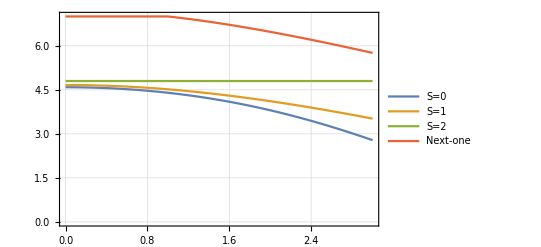

```mathematica
ListLinePlot[{e0data[[1;;31,1;;2]],e1data[[1;;31,1;;2]],e2data[[1;;31,1;;2]],e3data[[1;;31,1;;2]]},PlotLegends->{"S=0","S=1","S=2","Next-one"},PlotRange->All,Frame->True,GridLines->Automatic]
```

```mathematica
e1data//MatrixForm
```

(0. | 4.66369 | 2.
0.1 | 4.6622 | 2.
0.2 | 4.65774 | 2.
0.3 | 4.65031 | 2.
0.4 | 4.63993 | 2.
0.5 | 4.62664 | 2.
0.6 | 4.61047 | 2.
0.7 | 4.59145 | 2.
0.8 | 4.56964 | 2.
0.9 | 4.54509 | 2.
1. | 4.51786 | 2.
1.1 | 4.488 | 2.
1.2 | 4.45559 | 2.
1.3 | 4.42069 | 2.
1.4 | 4.38338 | 2.
1.5 | 4.34373 | 2.
1.6 | 4.30182 | 2.
1.7 | 4.25772 | 2.
1.8 | 4.2115 | 2.
1.9 | 4.16325 | 2.
2. | 4.11304 | 2.)

```mathematica
e2data//MatrixForm
```

(0. | 4.8 | 6.
0.1 | 4.8 | 6.
0.2 | 4.8 | 6.
0.3 | 4.8 | 6.
0.4 | 4.8 | 6.
0.5 | 4.8 | 6.
0.6 | 4.8 | 6.
0.7 | 4.8 | 6.
0.8 | 4.8 | 6.
0.9 | 4.8 | 6.
1. | 4.8 | 6.
1.1 | 4.8 | 6.
1.2 | 4.8 | 6.
1.3 | 4.8 | 6.
1.4 | 4.8 | 6.
1.5 | 4.8 | 6.
1.6 | 4.8 | 6.
1.7 | 4.8 | 6.
1.8 | 4.8 | 6.
1.9 | 4.8 | 6.
2. | 4.8 | 6.
2.1 | 4.8 | 6.
2.2 | 4.8 | 6.
2.3 | 4.8 | 6.
2.4 | 4.8 | 6.
2.5 | 4.8 | 6.
2.6 | 4.8 | 6.
2.7 | 4.8 | 6.
2.8 | 4.8 | 6.
2.9 | 4.8 | 6.
3. | 4.8 | 6.)

```mathematica
e3data//MatrixForm
```

(0. | 7. | 2.
0.1 | 7. | 2.
0.2 | 7. | 2.
0.3 | 7. | 2.
0.4 | 7. | 2.
0.5 | 7. | 2.
0.6 | 7. | 2.
0.7 | 7. | 2.
0.8 | 7. | 2.
0.9 | 7. | 2.
1. | 7. | 2.
1.1 | 6.95992 | 2.
1.2 | 6.91672 | 2.
1.3 | 6.87053 | 2.
1.4 | 6.82151 | 2.
1.5 | 6.76981 | 2.
1.6 | 6.71556 | 2.
1.7 | 6.65891 | 2.
1.8 | 6.6 | 2.
1.9 | 6.53895 | 2.
2. | 6.4759 | 2.
2.1 | 6.41096 | 2.
2.2 | 6.34424 | 2.
2.3 | 6.27585 | 2.
2.4 | 6.20589 | 2.
2.5 | 6.13446 | 2.
2.6 | 6.06164 | 2.
2.7 | 5.98752 | 2.
2.8 | 5.91218 | 2.
2.9 | 5.83569 | 2.
3. | 5.75813 | 2.)

```mathematica
jj1 = Table[{e0data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e0data][[1]]}]
```

{{0.,0.0681542},{0.1,0.0688991},{0.2,0.071132},{0.3,0.0748468},{0.4,0.0800337},{0.5,0.0866791},{0.6,0.0947659},{0.7,0.104274},{0.8,0.115178},{0.9,0.127454},{1.,0.141071},{1.1,0.155999},{1.2,0.172205},{1.3,0.189653},{1.4,0.208308},{1.5,0.228133},{1.6,0.24909},{1.7,0.271141},{1.8,0.294249},{1.9,0.318374},{2.,0.34348},{2.1,0.369528},{2.2,0.396483},{2.3,0.424307},{2.4,0.452965},{2.5,0.482424},{2.6,0.51265},{2.7,0.54361},{2.8,0.575273},{2.9,0.607609},{3.,0.640589}}

```mathematica
jj2 = Table[{e0data[[i,1]],((e0data[[i,2]])/3 ) +((e2data[[i,2]])/6)-((e1data[[i,2]])/2) },{i,1,Dimensions[e0data][[1]]}]
```

{{0.,-0.00217961},{0.1,-0.00205279},{0.2,-0.0016759},{0.3,-0.00105949},{0.4,-0.000220954},{0.5,0.000815753},{0.6,0.00202058},{0.7,0.00335787},{0.8,0.00478702},{0.9,0.00626318},{1.,0.00773809},{1.1,0.00916092},{1.2,0.0104792},{1.3,0.0116399},{1.4,0.0125902},{1.5,0.0132786},{1.6,0.0136556},{1.7,0.013675},{1.8,0.0132942},{1.9,0.0124748},{2.,0.0111837},{2.1,0.00939279},{2.2,0.00707944},{2.3,0.00422658},{2.4,0.000822542},{2.5,-0.00313913},{2.6,-0.00766001},{2.7,-0.0127372},{2.8,-0.0183637},{2.9,-0.0245292},{3.,-0.0312203}}

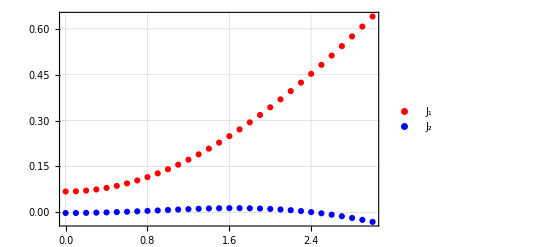

```mathematica
ListPlot[{jj1,jj2},PlotRange->Automatic,GridLines->Automatic,Frame->True,PlotLegends->Placed[{"J_1","J_2"},{Left,Center}],PlotStyle->{Red,Blue}]
```

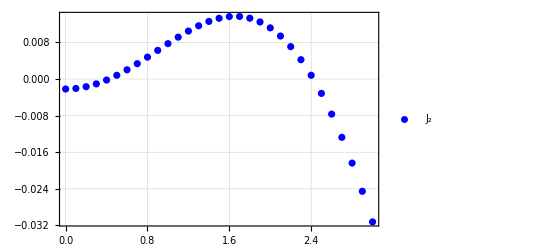

```mathematica
ListPlot[{jj2},PlotRange->Automatic,GridLines->Automatic,Frame->True,Frame->True,PlotLegends->Placed[{"J_2"},{Left,Center}],PlotStyle->Blue]
```

```mathematica
beta= Table[{e0data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[e0data][[1]]}]
```

{{0.,0.0319805},{0.1,0.0297942},{0.2,0.0235604},{0.3,0.0141554},{0.4,0.00276077},{0.5,-0.00941119},{0.6,-0.0213218},{0.7,-0.0322025},{0.8,-0.0415618},{0.9,-0.0491407},{1.,-0.0548523},{1.1,-0.0587241},{1.2,-0.0608534},{1.3,-0.061375},{1.4,-0.0604406},{1.5,-0.0582056},{1.6,-0.0548222},{1.7,-0.0504351},{1.8,-0.04518},{1.9,-0.0391829},{2.,-0.03256},{2.1,-0.0254183},{2.2,-0.0178556},{2.3,-0.00996114},{2.4,-0.0018159},{2.5,0.006507},{2.6,0.014942},{2.7,0.0234307},{2.8,0.0319218},{2.9,0.0403701},{3.,0.0487369}}

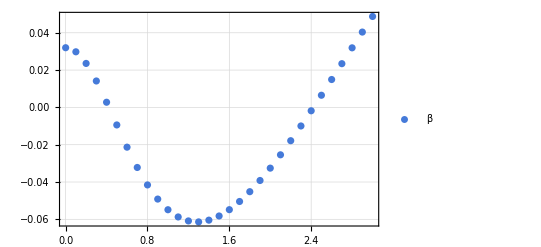

```mathematica
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotStyle->RGBColor[0.27,0.48,0.85],PlotLegends->Placed[{"β"},{Left,Center}]]
```